# Funktionen

Bitte für die Audiospur folgenden Link
https://www.carl-firle.eu/wp-content/uploads/2024/03/Einfuehrung-in-Mathematica-3-1.mp3
abrufen (oder das GitHub-Audioverzeichnis nutzen)

```mathematica
d=Import["C:\\Users\\mona_\\CloudStation\\Programmierung\\Mathematica\\Beispieldatei für Rebekka.xlsx"][[1]]
```

{{Name,Wert 1,Wert 2,Beschreibung,Eingeschlossen},{Maya,22.,23.,klein,Ja},{Kai,32.,33.,groß,Ja},{Gustaf,42.,43.,klein,Nein},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein},{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}}

```mathematica
Table["kopieren",5]
```

{kopieren,kopieren,kopieren,kopieren,kopieren}

```mathematica
Table[2,6]
```

{2,2,2,2,2,2}

```mathematica
Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[Prime[i],{i,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
Table[Sqrt[x],{x,{1,4,9,16}}]
```

{1,2,3,4}

```mathematica
Map[Sqrt[#]&,{1,4,9,16}]
```

{1,2,3,4}

```mathematica
Map[Sqrt,{1,4,9,16}]
```

{1,2,3,4}

```mathematica
Sqrt/@{1,4,9,16}
```

{1,2,3,4}

```mathematica
dT=Transpose@d
Map[Rest[#]&,dT2]
```

{{Name,Maya,Kai,Gustaf,Herbert,Maria,Insa,Friedrich},{Wert 1,22.,32.,42.,52.,62.,72.,82.},{Wert 2,23.,33.,43.,53.,63.,73.,83.},{Beschreibung,klein,groß,klein,groß,groß,klein,klein},{Eingeschlossen,Ja,Ja,Nein,Ja,Nein,Ja,Ja}}

{{Maya,Kai,Gustaf,Herbert,Maria,Insa,Friedrich},{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.},{klein,groß,klein,groß,groß,klein,klein},{Ja,Ja,Nein,Ja,Nein,Ja,Ja}}

```mathematica
dT2=Map[Rest,dT2]
```

{{Maya,Kai,Gustaf,Herbert,Maria,Insa,Friedrich},{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.},{klein,groß,klein,groß,groß,klein,klein},{Ja,Ja,Nein,Ja,Nein,Ja,Ja}}

```mathematica
Map[Reverse,dT2]
```

{{Friedrich,Insa,Maria,Herbert,Gustaf,Kai,Maya},{82.,72.,62.,52.,42.,32.,22.},{83.,73.,63.,53.,43.,33.,23.},{klein,klein,groß,groß,klein,groß,klein},{Ja,Ja,Nein,Ja,Nein,Ja,Ja}}

```mathematica
Map[Sort,dT2]
```

{{Friedrich,Gustaf,Herbert,Insa,Kai,Maria,Maya},{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.},{groß,groß,groß,klein,klein,klein,klein},{Ja,Ja,Ja,Ja,Ja,Nein,Nein}}

```mathematica
Map[Gather,dT2]
```

{{{Maya},{Kai},{Gustaf},{Herbert},{Maria},{Insa},{Friedrich}},{{22.},{32.},{42.},{52.},{62.},{72.},{82.}},{{23.},{33.},{43.},{53.},{63.},{73.},{83.}},{{klein,klein,klein,klein},{groß,groß,groß}},{{Ja,Ja,Ja,Ja,Ja},{Nein,Nein}}}

```mathematica
Map[Length,dT2]
```

{7,7,7,7,7}

```mathematica
Length/@dT2
```

{7,7,7,7,7}

```mathematica
Map[#[[1]]&,dT2]
```

{Maya,22.,23.,klein,Ja}

```mathematica
Map[#[[-1]]&,dT2]
```

{Friedrich,82.,83.,klein,Ja}

```mathematica
dT2[[All,-1]]
```

{Friedrich,82.,83.,klein,Ja}

```mathematica
Map[{#[[2]],#[[3]],#[[1]]}&,dT2]
```

{{Kai,Gustaf,Maya},{32.,42.,22.},{33.,43.,23.},{groß,klein,klein},{Ja,Nein,Ja}}

```mathematica
dT2[[All,{2,3,1}]]
```

{{Kai,Gustaf,Maya},{32.,42.,22.},{33.,43.,23.},{groß,klein,klein},{Ja,Nein,Ja}}

```mathematica
dT2[[{2,3},All]]
Map[{#[[1]]/5,#[[2]]/88,#[[3]]/12,#[[4]],#[[5]],#[[6]]-3}&,dT2[[{2,3},All]]]
```

{{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.}}

{{4.4,0.363636,3.5,52.,62.,69.},{4.6,0.375,3.58333,53.,63.,70.}}

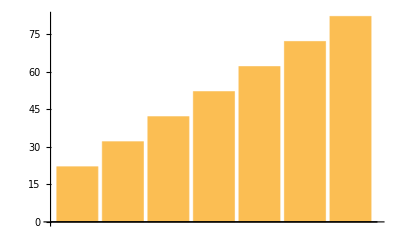
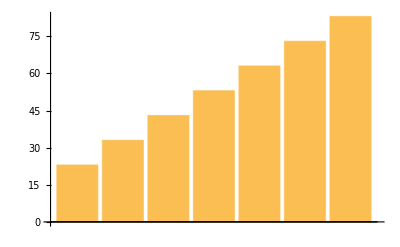

```mathematica
Map[BarChart[#]&,dT2[[{2,3},All]]]
```

```mathematica
Table[BarChart[i],{i,dT2[[{2,3},All]]}]
```

{-Graphics-,-Graphics-}

Bitte für die Audiospur folgenden Link
https://www.carl-firle.eu/wp-content/uploads/2024/03/Einfuehrung-in-Mathematica-3-2.mp3
abrufen (oder das GitHub-Audioverzeichnis nutzen)

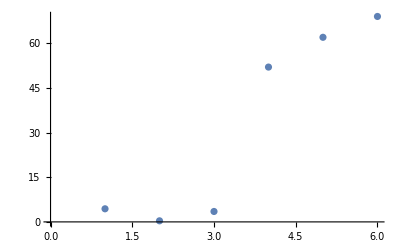
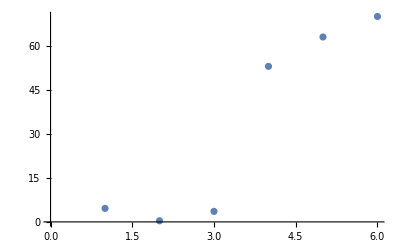

{-Graphics-,-Graphics-}

```mathematica
temp=Map[{#[[1]]/5,#[[2]]/88,#[[3]]/12,#[[4]],#[[5]],#[[6]]-3}&,dT2[[{2,3},All]]];
Map[ListPlot[#]&,temp]
ListPlot/@temp
```

```mathematica
Map[#/Max[#]&,dT2[[{2,3},All]]]
```

{{0.268293,0.390244,0.512195,0.634146,0.756098,0.878049,1.},{0.277108,0.39759,0.518072,0.638554,0.759036,0.879518,1.}}

```mathematica
Map[{#/Max[#],#/Min[#]}&,dT2[[{2,3},All]]]
```

{{{0.268293,0.390244,0.512195,0.634146,0.756098,0.878049,1.},{1.,1.45455,1.90909,2.36364,2.81818,3.27273,3.72727}},{{0.277108,0.39759,0.518072,0.638554,0.759036,0.879518,1.},{1.,1.43478,1.86957,2.30435,2.73913,3.17391,3.6087}}}

{{{0.268293,1.},{0.390244,1.45455},{0.512195,1.90909},{0.634146,2.36364},{0.756098,2.81818},{0.878049,3.27273},{1.,3.72727}},{{0.277108,1.},{0.39759,1.43478},{0.518072,1.86957},{0.638554,2.30435},{0.759036,2.73913},{0.879518,3.17391},{1.,3.6087}}}

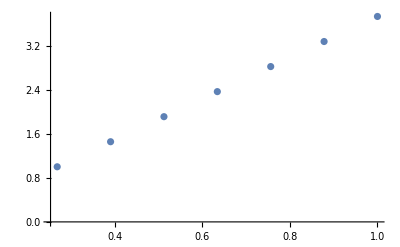
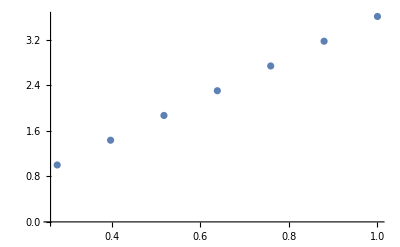

```mathematica
temp=Map[Transpose[{#/Max[#],#/Min[#]}]&,dT2[[{2,3},All]]]
ListPlot/@temp
```

```mathematica
temp=Map[Transpose[{#,#/Max[#],#/Min[#]}]&,dT2[[{2,3},All]]]
TableForm[temp]
TableForm/@temp
```

{{{22.,0.268293,1.},{32.,0.390244,1.45455},{42.,0.512195,1.90909},{52.,0.634146,2.36364},{62.,0.756098,2.81818},{72.,0.878049,3.27273},{82.,1.,3.72727}},{{23.,0.277108,1.},{33.,0.39759,1.43478},{43.,0.518072,1.86957},{53.,0.638554,2.30435},{63.,0.759036,2.73913},{73.,0.879518,3.17391},{83.,1.,3.6087}}}

22.
0.268293
1. | 32.
0.390244
1.45455 | 42.
0.512195
1.90909 | 52.
0.634146
2.36364 | 62.
0.756098
2.81818 | 72.
0.878049
3.27273 | 82.
1.
3.72727
23.
0.277108
1. | 33.
0.39759
1.43478 | 43.
0.518072
1.86957 | 53.
0.638554
2.30435 | 63.
0.759036
2.73913 | 73.
0.879518
3.17391 | 83.
1.
3.6087

{22. | 0.268293 | 1.
32. | 0.390244 | 1.45455
42. | 0.512195 | 1.90909
52. | 0.634146 | 2.36364
62. | 0.756098 | 2.81818
72. | 0.878049 | 3.27273
82. | 1. | 3.72727,23. | 0.277108 | 1.
33. | 0.39759 | 1.43478
43. | 0.518072 | 1.86957
53. | 0.638554 | 2.30435
63. | 0.759036 | 2.73913
73. | 0.879518 | 3.17391
83. | 1. | 3.6087}

```mathematica
Map[(a+#)&,dT2[[{2,3},All]]]
```

{{22.+a,32.+a,42.+a,52.+a,62.+a,72.+a,82.+a},{23.+a,33.+a,43.+a,53.+a,63.+a,73.+a,83.+a}}

```mathematica
dT2[[{2,3},All]]
a=1
Map[(a=a*10;a+#)&,dT2[[{2,3},All]]]
```

{{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.}}

1

{{32.,42.,52.,62.,72.,82.,92.},{123.,133.,143.,153.,163.,173.,183.}}

Bitte für die Audiospur folgenden Link
https://www.carl-firle.eu/wp-content/uploads/2024/03/Einfuehrung-in-Mathematica-3-3.mp3
abrufen (oder das GitHub-Audioverzeichnis nutzen)

```mathematica
dT2[[{2,3},All]]
a=1
Map[(a=a*10/#[[1]];a+#)&,dT2[[{2,3},All]]]
```

{{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.}}

1

{{22.4545,32.4545,42.4545,52.4545,62.4545,72.4545,82.4545},{23.1976,33.1976,43.1976,53.1976,63.1976,73.1976,83.1976}}

```mathematica
Rest[d]
```

{{Maya,22.,23.,klein,Ja},{Kai,32.,33.,groß,Ja},{Gustaf,42.,43.,klein,Nein},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein},{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}}

```mathematica
SortBy[Rest[d],#[[-1]]&]
```

{{Friedrich,82.,83.,klein,Ja},{Herbert,52.,53.,groß,Ja},{Insa,72.,73.,klein,Ja},{Kai,32.,33.,groß,Ja},{Maya,22.,23.,klein,Ja},{Gustaf,42.,43.,klein,Nein},{Maria,62.,63.,groß,Nein}}

```mathematica
SortBy[Rest[d],Last]
```

{{Friedrich,82.,83.,klein,Ja},{Herbert,52.,53.,groß,Ja},{Insa,72.,73.,klein,Ja},{Kai,32.,33.,groß,Ja},{Maya,22.,23.,klein,Ja},{Gustaf,42.,43.,klein,Nein},{Maria,62.,63.,groß,Nein}}

```mathematica
SplitBy[Rest[d],Last]
```

{{{Maya,22.,23.,klein,Ja},{Kai,32.,33.,groß,Ja}},{{Gustaf,42.,43.,klein,Nein}},{{Herbert,52.,53.,groß,Ja}},{{Maria,62.,63.,groß,Nein}},{{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}}}

```mathematica
SplitBy[SortBy[Rest[d],Last],Last]
```

{{{Friedrich,82.,83.,klein,Ja},{Herbert,52.,53.,groß,Ja},{Insa,72.,73.,klein,Ja},{Kai,32.,33.,groß,Ja},{Maya,22.,23.,klein,Ja}},{{Gustaf,42.,43.,klein,Nein},{Maria,62.,63.,groß,Nein}}}

```mathematica
GatherBy[Rest[d],Last]
```

{{{Maya,22.,23.,klein,Ja},{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}},{{Gustaf,42.,43.,klein,Nein},{Maria,62.,63.,groß,Nein}}}

```mathematica
temp=Table[GatherBy[Rest[d],#[[i]]&],{i,{-1,-2}}]
```

{{{{Maya,22.,23.,klein,Ja},{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}},{{Gustaf,42.,43.,klein,Nein},{Maria,62.,63.,groß,Nein}}},{{{Maya,22.,23.,klein,Ja},{Gustaf,42.,43.,klein,Nein},{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}},{{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein}}}}

```mathematica
temp[[All,2]]
temp[[All,2]][[All,All,1]]
Intersection@@%
```

{{{Gustaf,42.,43.,klein,Nein},{Maria,62.,63.,groß,Nein}},{{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein}}}

{{Gustaf,Maria},{Kai,Herbert,Maria}}

{Maria}

```mathematica
Select[Rest[d],#[[2]]<60&]
```

{{Maya,22.,23.,klein,Ja},{Kai,32.,33.,groß,Ja},{Gustaf,42.,43.,klein,Nein},{Herbert,52.,53.,groß,Ja}}

```mathematica
Select[Rest[d],Equal[#[[4]],"groß"]&]
```

{{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein}}

```mathematica
Select[Rest[d],#[[4]]=="groß"&]
```

{{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein}}

```mathematica
Select[Rest[d],#[[4]]!="groß"&]
```

{{Maya,22.,23.,klein,Ja},{Gustaf,42.,43.,klein,Nein},{Insa,72.,73.,klein,Ja},{Friedrich,82.,83.,klein,Ja}}

```mathematica
Select[Rest[d],#[[-1]]=="Nein"&&#[[-2]]=="groß"&]
```

{{Maria,62.,63.,groß,Nein}}

```mathematica
Select[Rest[d],#[[-1]]=="Nein"||#[[-2]]=="groß"&]
```

{{Kai,32.,33.,groß,Ja},{Gustaf,42.,43.,klein,Nein},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein}}

```mathematica
Select[Rest[d],#[[4]]==="groß"&]
```

{{Kai,32.,33.,groß,Ja},{Herbert,52.,53.,groß,Ja},{Maria,62.,63.,groß,Nein}}

Bitte für die Audiospur folgenden Link
https://www.carl-firle.eu/wp-content/uploads/2024/03/Einfuehrung-in-Mathematica-3-4.mp3
abrufen (oder das GitHub-Audioverzeichnis nutzen)

```mathematica
SameQ[0.,0]
```

False

```mathematica
Equal[0.,0]
```

True

```mathematica
{0.===0,0.==0}
```

{False,True}

```mathematica
Head[0.]
```

Real

```mathematica
Head[0]
```

Integer

```mathematica
Head["groß"]
```

String

```mathematica
Head[{"Herbert",52.,53.,"groß","Ja"}]
```

List

```mathematica
IntegerQ[2.3]
```

False

```mathematica
IntegerQ/@{3.2,3,5,9.2,10}
```

{False,True,True,False,True}

```mathematica
StringQ/@{"Rebekka","Carl",3,12,"Nina",π}
```

{True,True,False,False,True,False}

```mathematica
StringQ/@{"Rebekka","Carl",ToString@3,ToString@12,"Nina",ToString@π}
```

{True,True,True,True,True,True}

```mathematica
dT2
```

{{Maya,Kai,Gustaf,Herbert,Maria,Insa,Friedrich},{22.,32.,42.,52.,62.,72.,82.},{23.,33.,43.,53.,63.,73.,83.},{klein,groß,klein,groß,groß,klein,klein},{Ja,Ja,Nein,Ja,Nein,Ja,Ja}}

```mathematica
dT2[[2]]
If[#>50,Framed[#],#]&/@dT2[[2]]
```

{22.,32.,42.,52.,62.,72.,82.}

{22.,32.,42.,52.,62.,72.,82.}

```mathematica
If[#>50,#/20,#*99]&/@dT2[[2]]
```

{2178.,3168.,4158.,2.6,3.1,3.6,4.1}

```mathematica
Which[#>50,#/20,#<30,#-66,NumberQ[#],"passt"]&/@dT2[[2]]
```

{-44.,passt,passt,2.6,3.1,3.6,4.1}

```mathematica
myFunction[l_List]:=Module[{},Which[#>50,#/20,#<30,#-66,NumberQ[#],"passt"]&/@l]
```

```mathematica
myFunction[dT2[[2]]]
```

{-44.,passt,passt,2.6,3.1,3.6,4.1}

```mathematica
myFunction[dT2[[3]]]
```

{-43.,passt,passt,2.65,3.15,3.65,4.15}

```mathematica
myFunction/@dT2[[2;;3]]
```

{{-44.,passt,passt,2.6,3.1,3.6,4.1},{-43.,passt,passt,2.65,3.15,3.65,4.15}}